```mathematica
SetDirectory[NotebookDirectory[]];dataJson=Association@Import["decoded_data.json"];
```

```mathematica
Keys@dataJson
```

{basic_data,types_products_count,products_data,warehouses_count,warehouses_data,orders_count,orders_data}

## 1

```mathematica
d1=Association@dataJson⟦"basic_data"⟧;
rows=d1["rows"];
columns=d1["columns"];
numberOfDrones=d1["drones"];
turnsOfDrones=d1["turns"];
capacityOfDrones=d1["max_payload"];
numberOfProducts=dataJson["types_products_count"];
numberOfWarehouses=dataJson["warehouses_count"];
numberOfOrders=dataJson["orders_count"];
```

## 2

```mathematica
productsWeights=Last/@dataJson["products_data"];
```

## 3

```mathematica
d3=dataJson["warehouses_data"];
```

```mathematica
warehousesCoords=d3⟦All,2,1,2⟧;
```

```mathematica
productsInWarehouses=d3⟦All,2,2,2,All,2⟧;
```

## 4

```mathematica
d4=dataJson["orders_data"]
```

{0→{coords→{340,371},count_products→8,product_types→{226,183,6,220,299,280,12,42}},1248,1249→{coords→{157,157},count_products→4,product_types→{385,258,15,40}}}
 |  |  |  |

```mathematica
ordersCoords=d4⟦All,2,1,2⟧;
```

```mathematica
orders=ConstantArray[0,{numberOfOrders,numberOfProducts}];
```

```mathematica
ordersLists=d4⟦All,2,3,2⟧
```

{{226,183,6,220,299,280,12,42},{163},{192,81},{270,305,111,37,219,111,96,290,377,113},1242,{362,283,356,58,361,57,377,302},{348,364,293,260,200,288,43,384,32,6,214,351,163,360},{244,62,265,344,185},{385,258,15,40}}
 |  |  |  |

```mathematica
orders=ConstantArray[0,{numberOfOrders,numberOfProducts}];
Do[
orders⟦i,j+1⟧+=1
,{i,Length@ordersLists},{j,ordersLists⟦i⟧}];
```

```mathematica
ordersLists
```

{{226,183,6,220,299,280,12,42},{163},{192,81},{270,305,111,37,219,111,96,290,377,113},1242,{362,283,356,58,361,57,377,302},{348,364,293,260,200,288,43,384,32,6,214,351,163,360},{244,62,265,344,185},{385,258,15,40}}
 |  |  |  |

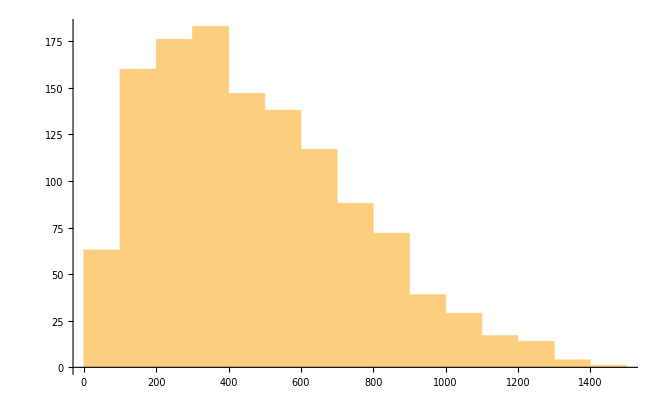

```mathematica
Histogram[Total@productsWeights⟦#⟧&/@ordersLists]
```